```mathematica
(* cusp parameters for ϕ=0 *)
```

```mathematica
b=(√(1-2 k^2))/k;
p=b^2/(√(1+b^2));
q=0;
```

```mathematica
(* change coordinates *)
τ->(√(b^4+p^2))/(b p)w;
w->(b p)/(√(b^4+p^2))τ;
σ->(2EllipticK[k^2])/π r;
r->π/(2EllipticK[k^2])σ;
```

```mathematica
(* regularized volume *)
T ((Integrate[1/Cos[r]^2,r]/.{r-> ArcTan[Sinh[ρ0]]})-(Integrate[1/Cos[r]^2,r]/.{r->-ArcTan[Sinh[ρ0]]}))//FullSimplify//PowerExpand
```

2 T Sinh[ρ0]

```mathematica
(* JacobiSN *)
```

```mathematica
tmp=JacobiSN[u,k^2]//Series[#,{u,0,40}]&//Normal;
tmp=tmp/.{u->(2 EllipticK[k^2])/π r}//Series[#,{k,0,2}]&;
tmp//Collect[#,{k^2},Expand]&;

tmp-(Sin[r]+(Sin[r] Cos[r]^2)/4 k^2)//Series[#,{r,0,40}]&//Collect[#,{k^2},Expand]&
```

0

```mathematica
(* JacobiCN *)
```

```mathematica
tmp=JacobiCN[u,k^2]//Series[#,{u,0,40}]&//Normal;
tmp=tmp/.{u->(2 EllipticK[k^2])/π r}//Series[#,{k,0,2}]&;
tmp//Collect[#,{k^2},Expand]&;

tmp-(Cos[r]-(Sin[r]^2 Cos[r])/4 k^2)//Series[#,{r,0,40}]&//Collect[#,{k^2},Expand]&
```

0

```mathematica
(* JacobiDN *)
```

```mathematica
tmp=JacobiDN[u,k^2]//Series[#,{u,0,40}]&//Normal;
tmp=tmp/.{u->(2 EllipticK[k^2])/π r}//Series[#,{k,0,2}]&;
tmp//Collect[#,{k^2},Expand]&;

tmp-(1-Sin[r]^2/2 k^2)//Series[#,{r,0,40}]&//Collect[#,{k^2},Expand]&
```

0

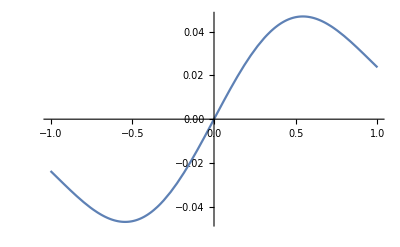

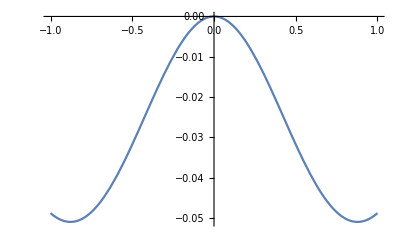

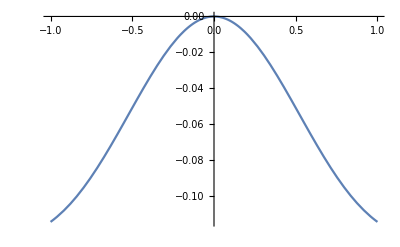

```mathematica
Plot[(JacobiSN[(2 EllipticK[k^2])/π r,k^2]-(Sin[r]+(Sin[r] Cos[r]^2)/4 k^2))/k^4/.k->10^-6,{r,-1,1},WorkingPrecision->100]
Plot[(JacobiCN[(2 EllipticK[k^2])/π r,k^2]-(Cos[r]-(Sin[r]^2 Cos[r])/4 k^2))/k^4/.k->10^-6,{r,-1,1},WorkingPrecision->100]
Plot[(JacobiDN[(2 EllipticK[k^2])/π r,k^2]-(1-Sin[r]^2/2 k^2))/k^4/.k->10^-6,{r,-1,1},WorkingPrecision->100]
```

```mathematica
(* Δ EllipticPi *)
```

```mathematica
tmp=p^2/(b √(b^4+p^2))(1-b^4/(b^4+p^2)Cos[t]^2)^-1(1-k^2 Cos[t]^2)^(-1/2)//Series[#,{k,0,2}]&//Simplify//Normal
tmp=Integrate[tmp,t]//Collect[#,k^2,Simplify]&
(tmp/.t->σ)-(tmp/.t->0)//Collect[#,k^2,Simplify]&
```

k Csc[t]^2

-k Cot[t]

ComplexInfinity

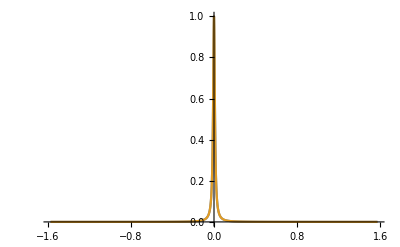

```mathematica
tmp1=-p^2/(b √(b^4+p^2))D[-EllipticPi[b^4/(b^4+p^2),σ+π/2,k^2]+EllipticPi[b^4/(b^4+p^2),k^2],σ]//Simplify;
tmp2=p^2/(b √(b^4+p^2))(1-b^4/(b^4+p^2)Cos[t]^2)^-1(1-k^2 Cos[t]^2)^(-1/2)/.t->σ;

k=10^-2;
Plot[{k tmp1,k tmp2},{σ,-EllipticK[k^2],EllipticK[k^2]},PlotRange->All]
Clear[k]
```

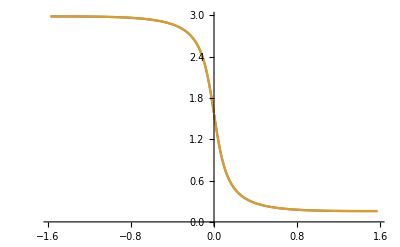

```mathematica
tmp1=π/2+p^2/(b √(b^4+p^2))(σ-EllipticPi[b^4/(b^4+p^2),σ+π/2,k^2]+EllipticPi[b^4/(b^4+p^2),k^2]);
tmp2=tmp1=π/2+(p^2/(b √(b^4+p^2))σ-p^2/(b √(b^4+p^2))EllipticPi[b^4/(b^4+p^2),σ+π/2,k^2]+p^2/(b √(b^4+p^2))EllipticPi[b^4/(b^4+p^2),k^2]);;

k=10^-1;
Plot[{tmp1,tmp2},{σ,-EllipticK[k^2],EllipticK[k^2]}]
Clear[k]
```

```mathematica
π/2+p^2/(b √(b^4+p^2))(σ-(am2/k^2+a0+a2 k^2+a4 k^4))//Series[#,{k,0,2}]&
```

-am2/k+π/2+(-a0+am2/2+σ) k+O[k]^3

```mathematica
(* check metric k=0 *)
```

```mathematica
tmp=(1-k^2)/(JacobiCN[(2 EllipticK[k^2])/π r,k^2]^2)(((2 EllipticK[k^2])/π)^2 dr^2+Simplify[(b^4+p^2)/(b^2 p^2)] dw^2);

tmp== (dr^2+dw^2)/Cos[r]^2/.k->0
```

True

### Metric g_ij, vielbein (e^a)_i and inverse E_i^a

```mathematica
coord={r,w};

g=1/Cos[r]^2({{1, 0}, {0, 1}}); (* g[i,j] *)
ginv=Inverse[g];
vielbein=√g;//PowerExpand; (* e[a,i] *)
invvielbein=√ginv//PowerExpand; (* E[i,a] *)
```

### Christoffel symbols (Γ^i)_kl and spin connection (ω^ab)_i=(e^a)_j(e^b)_k(ω^jk)_i

```mathematica
Γ[i_,k_,l_]:=Γ[i,k,l]=Sum[ginv[[i,m]]/2(D[g[[m,k]],coord[[l]]]+D[g[[m,l]],coord[[k]]]-D[g[[k,l]],coord[[m]]]),{m,2}]

Table[{{i,j,k},Γ[i,j,k]},{i,2},{j,2},{k,2}]//MatrixForm
```

(({1,1,1} | Tan[r]
{1,1,2} | 0) | ({1,2,1} | 0
{1,2,2} | -Tan[r])
({2,1,1} | 0
{2,1,2} | Tan[r]) | ({2,2,1} | Tan[r]
{2,2,2} | 0))

```mathematica
ω[a_,b_,i_]:=ω[a,b,i]=(Sum[KroneckerDelta[b,d]vielbein[[a,j]] D[invvielbein[[j,d]],coord[[i]]],{j,2},{d,2}]+
Sum[KroneckerDelta[b,d]vielbein[[a,j]] Γ[j,i,p] invvielbein[[p,d]],{j,2},{p,2},{d,2}])

Table[{{a,b,i},ω[a,b,i]},{a,2},{b,2},{i,2}]//PowerExpand//MatrixForm
```

(({1,1,1} | 0
{1,1,2} | 0) | ({1,2,1} | 0
{1,2,2} | -Tan[r])
({2,1,1} | 0
{2,1,2} | Tan[r]) | ({2,2,1} | 0
{2,2,2} | 0))

### Killing vectors

```mathematica
ξ1={Cos[r] Sinh[w],- Sin[r]Cosh[w]};
ξ2={0,1};
ξ3={Cos[r] Cosh[w],-Sin[r] Sinh[w]};

Table[Sum[ξ1[[i]] D[g[[a,b]],coord[[i]]]+g[[i,b]]D[ξ1[[i]] ,coord[[a]]]+g[[i,a]]D[ξ1[[i]] ,coord[[b]]],{i,2}],{a,2},{b,2}]//Simplify//MatrixForm

Table[Sum[ξ2[[i]] D[g[[a,b]],coord[[i]]]+g[[i,b]]D[ξ2[[i]] ,coord[[a]]]+g[[i,a]]D[ξ2[[i]] ,coord[[b]]],{i,2}],{a,2},{b,2}]//Simplify//MatrixForm

Table[Sum[ξ3[[i]] D[g[[a,b]],coord[[i]]]+g[[i,b]]D[ξ3[[i]] ,coord[[a]]]+g[[i,a]]D[ξ3[[i]] ,coord[[b]]],{i,2}],{a,2},{b,2}]//Simplify//MatrixForm
```

(0 | 0
0 | 0)

(0 | 0
0 | 0)

(0 | 0
0 | 0)

```mathematica
Sum[ξ1[[j]]D[ξ2[[i]]D[f[ρ,τ],coord[[i]]],coord[[j]]]-ξ2[[j]]D[ξ1[[i]]D[f[ρ,τ],coord[[i]]],coord[[j]]],{i,2},{j,2}]==-Sum[ξ3[[i]]D[f[ρ,τ],coord[[i]]],{i,2}]//Simplify

Sum[ξ1[[j]]D[ξ3[[i]]D[f[ρ,τ],coord[[i]]],coord[[j]]]-ξ3[[j]]D[ξ1[[i]]D[f[ρ,τ],coord[[i]]],coord[[j]]],{i,2},{j,2}]==Sum[ξ2[[i]]D[f[ρ,τ],coord[[i]]],{i,2}]//Simplify

Sum[ξ2[[j]]D[ξ3[[i]]D[f[ρ,τ],coord[[i]]],coord[[j]]]-ξ3[[j]]D[ξ2[[i]]D[f[ρ,τ],coord[[i]]],coord[[j]]],{i,2},{j,2}]==Sum[ξ1[[i]]D[f[ρ,τ],coord[[i]]],{i,2}]//Simplify
```

True

True

True

### Spinor parallel propagator

```mathematica
Γ[1]=PauliMatrix[1];
Γ[2]=PauliMatrix[2];
Γ[3]=PauliMatrix[3];

Γ[3]==-ⅈ Γ[1].Γ[2]
```

True

```mathematica
d[r_,w_,rp_,wp_]:=ArcCosh[-Tan[r]Tan[rp]+Cosh[w-wp]/(Cos[r]Cos[rp])]

θ[r_,w_,rp_,wp_]:= ArcTan[√((1+√((-1+1/4 Sec[r] (5 Cosh[w]-3 Sinh[w]))/(1+1/4 Sec[r] (5 Cosh[w]-3 Sinh[w]))) (1+1/4 Sec[r] (5 Cosh[w]-3 Sinh[w])) √((-1+1/4 Sec[rp] (5 Cosh[wp]-3 Sinh[wp]))/(1+1/4 Sec[rp] (5 Cosh[wp]-3 Sinh[wp]))) (1+1/4 Sec[rp] (5 Cosh[wp]-3 Sinh[wp]))+1/16 Sec[r] Sec[rp] (5 Cosh[w]-3 Sinh[w]) (5 Cosh[wp]-3 Sinh[wp]))/(1-√((-1+1/4 Sec[r] (5 Cosh[w]-3 Sinh[w]))/(1+1/4 Sec[r] (5 Cosh[w]-3 Sinh[w]))) (1+1/4 Sec[r] (5 Cosh[w]-3 Sinh[w])) √((-1+1/4 Sec[rp] (5 Cosh[wp]-3 Sinh[wp]))/(1+1/4 Sec[rp] (5 Cosh[wp]-3 Sinh[wp]))) (1+1/4 Sec[rp] (5 Cosh[wp]-3 Sinh[wp]))+1/16 Sec[r] Sec[rp] (5 Cosh[w]-3 Sinh[w]) (5 Cosh[wp]-3 Sinh[wp])))(-((4 Sin[rp] (3 Cosh[w]-5 Sinh[w]))/(√(-16 Cos[r]^2+(5 Cosh[w]-3 Sinh[w])^2) √(-16 Cos[rp]^2+(5 Cosh[wp]-3 Sinh[wp])^2)))+(4 Sin[r] (3 Cosh[wp]-5 Sinh[wp]))/(√(-16 Cos[r]^2+(5 Cosh[w]-3 Sinh[w])^2) √(-16 Cos[rp]^2+(5 Cosh[wp]-3 Sinh[wp])^2)))/(1+(16 Sin[r] Sin[rp])/(√(-16 Cos[r]^2+(5 Cosh[w]-3 Sinh[w])^2) √(-16 Cos[rp]^2+(5 Cosh[wp]-3 Sinh[wp])^2))+((3 Cosh[w]-5 Sinh[w]) (3 Cosh[wp]-5 Sinh[wp]))/(√(-16 Cos[r]^2+(5 Cosh[w]-3 Sinh[w])^2) √(-16 Cos[rp]^2+(5 Cosh[wp]-3 Sinh[wp])^2)))];

Λ[r_,w_]:=1/(√((5 Cosh[w]-3 Sinh[w])^2-16 Cos[r]^2))({{Sin[r](5 Cosh[w]-3 Sinh[w]), Cos[r](3 Cosh[w]-5 Sinh[w])}, {Cos[r](-3 Cosh[w]+5 Sinh[w]), Sin[r](5 Cosh[w]-3 Sinh[w])}})

δ[r_,w_]:=ArcTan[Λ[r,w][[1,1]],Λ[r,w][[1,2]]]

S[r_,w_]:=Cos[δ[r,w]/2] IdentityMatrix[2]+ ⅈ Γ[3] Sin[δ[r,w]/2] 

Sinv[r_,w_]:=Cos[δ[r,w]/2] IdentityMatrix[2]- ⅈ Γ[3] Sin[δ[r,w]/2] 

U[r_,w_,rp_,wp_]:=S[r,w].(IdentityMatrix[2] Cos[θ[r,w,rp,wp]]+ ⅈ Γ[3] Sin[θ[r,w,rp,wp]]).Sinv[rp,wp]
```

```mathematica
U[r,w,r,w]==IdentityMatrix[2]//Simplify
```

True

```mathematica
Do[{
tmprandom=Flatten[({{r->RandomReal[{-π/2,π/2}]}, {w->RandomReal[{-2,2}]}, {rp->RandomReal[{-π/2,π/2}]}, {wp->RandomReal[{-2,2}]}})];
Print[Table[D[U[r,w,rp,wp],coord[[i]]]+Sum[1/2 ω[a,b,i] ((Γ[a].Γ[b]-Γ[b].Γ[a])/4).U[r,w,rp,wp],{a,2},{b,2}]-Sum[Tanh[d[r,w,rp,wp]/2]vielbein[[a,i]]invvielbein[[j,b]]((Γ[a].Γ[b]-Γ[b].Γ[a])/4).U[r,w,rp,wp] D[d[r,w,rp,wp],coord[[j]]],{a,2},{b,2},{j,2}],{i,2}]/.tmprandom//Chop]
},{ii,50}]
```

{{{0,0},{0,0}},{{0,0},{0,0}}}

{{{0,0},{0,0}},{{0,0},{0,0}}}

{{{0,0},{0,0}},{{0,0},{0,0}}}

«47 more identical outputs»